```mathematica
fx[x_,t_]:=Sin[x-v1 t];
fy[y_,t_]:=Sin[y-v2 t];
v1=5; v2=5.5;
f[x_,y_,t_]:=fx[x,t]+fy[y,t];
Manipulate[DensityPlot[f[x,y,t],{x,-Pi,Pi},{y,-Pi,Pi}],{t,0,10}]
```

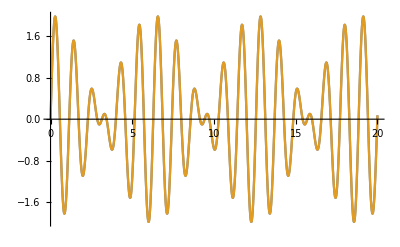

```mathematica
Plot[{f[Pi,Pi,t],f[-Pi,-Pi,t]},{t,0,20}]
```